# Running in the Rain

## Predicting Runs based on Environmental Data

Stephen Schroeder

## Introduction

I have been running for several years now, and in September of 2017 I decided that I would start a "run streak." A running streak is defined as running at least 1 mile (1.61 km) every calendar day consecutively. I did this mostly because I found that I couldn't stick to only running 3 or 4 days a week - I would suddenly find myself not having run for several weeks or months! 

Now, almost two years later I have ideas about things that might affect my running, but Wolfram Language allows for so much interesting analysis to be done with my data tracked using RunKeeper! Normally I don’t go out with a plan for how long I will run, and I turn back based on how I am feeling that day. Because of this, one of the main questions that I have about my running data is how my running is affected by temperature. I know that I run less in the Canadian winter, but exactly how much less?

## Running Data Preparation

### Importing Running Data

Previously, I used ServiceConnect to fetch my running data, but unfortunately ServiceConnect does not fetch GPS data from RunKeeper which I will need to be able to get environmental data based on the location, date, and time of my run. 
So, I manually exported my data from my RunKeeper account as explained here, and saved the data to my NotebookDirectory[] with all the GPS files in their own folder. Now, to get started, all the data needs to be imported. I imported the data in a similar fashion to this fantastic Wolfram Blog post, where the running data is parsed using the smart SemanticImport using the column types of the .csv file from RunKeeper.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
runningData = SemanticImport[
	"cardioActivities.csv",
	{"String","Date","String","String",Restricted["Quantity","Kilometers"],
	"String","String",Restricted["Quantity",("Kilometers")/("Hours")],Restricted["Quantity","LargeCalories"],
	Restricted["Quantity","Meters"],"String","String","String","String"
	}
];
```

The GPS Data is slightly more difficult to work with, as each of the 651 runs that I exported have their own .GPX file, and to best deal with the data I only want the coordinates that were recorded at the very beginning of the run.

```mathematica
importGPSData[] := importGPSData[FileNames["*.gpx", "GPS"]]
importGPSData[files_List] := Association@ Map[importGPSData, files]
importGPSData[file_String] :=FileNameTake[file] ->  First @ Cases[
Import[file, "XML"], XMLElement["trkpt",{"lat"->lat_,"lon"->lon_},{_,XMLElement["time",{},{time_}]}] :> {time, lat, lon}, 
Infinity
];

rawGPSData = importGPSData[];
```

Now, so I can best use the GPS data, I will make sure that it is explicitly made up of lists of GeoPositions

```mathematica
GPSData = Map[
GeoPosition@{ToExpression[#[[2]]], ToExpression[#[[3]]]} &, 
rawGPSData
];
```

Lastly, the data needs to be added alongside the rest of the running data imported earlier into our now nice looking dataset!

```mathematica
runningDataWithGPS = Map[
Append[#, "GeoCoord" -> GPSData[#["GPX File"]]]&,
runningData
];
```

### Getting Date-time and Location Specific Temperatures

In order to discover how temperature affects how long I run, I first need to get the data. Thankfully Location and Time-Specific Data is available using the Wolfram Language’s integrated knowledge. I’ll also clean up some missing GPS data to avoid errors.

```mathematica
coords = DeleteCases[Values@Normal@runningDataWithGPS[[All, {"GeoCoord", "Date"}]], {_Missing, _}];
tempData = AirTemperatureData[coords];
```

Finally, all that needs to be done is to add this data to the dataset!

```mathematica
tempDataAssoc = AssociationThread[coords -> tempData];
```

```mathematica
runningDataWithGPSandTemp = Map[
Append[#, "Temperature" -> tempDataAssoc[{#["GeoCoord"],#["Date"]}]]&,
runningDataWithGPS
];
```

```mathematica
DumpSave["fullrundata.mx",{runningDataWithGPSandTemp,coords,tempDataAssoc,tempData}];
```

```mathematica
Get["fullrundata.mx"];
```

## Data Visualisation and Evaluation

Now it' s possible to do tons of analysis of my running data! First, we can see the starting locations of my runs over the past  2 years. Lots of running in icy Canada.

```mathematica
geodata = Flatten[
			Cases[coords,GeoPosition[place__]:>{place},Infinity]
				,1];
```

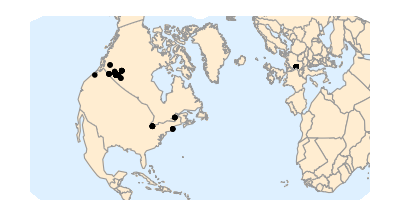

```mathematica
GeoGraphics[GeoMarker[geodata],GeoBackground->"CountryBorders"]
```

The next plot provides real evidence that those cold winters do cause my running distance to go down! It seems like there must be some correlation there.

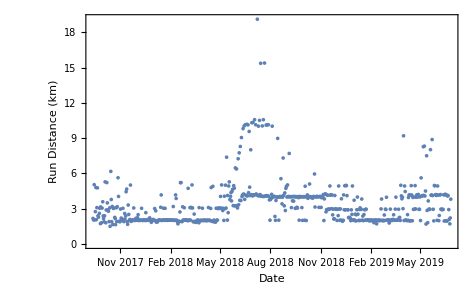

```mathematica
DateListPlot[Query[All,{"Date","Distance (km)"}]@runningDataWithGPSandTemp,Axes->True,FrameLabel->{"Date","Run Distance (km)"},Joined->False,PlotRange->All]
```

The next step is to determine pair the temperature at the time and location of my run with the distance of my run:

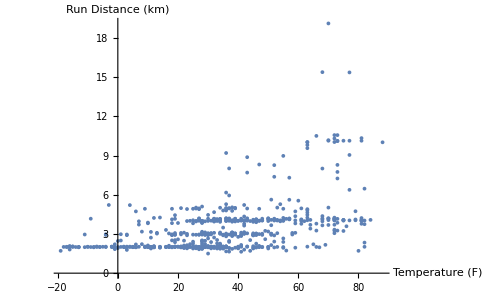

```mathematica
ListPlot[Query[All,{"Temperature","Distance (km)"}]@runningDataWithGPSandTemp,AxesLabel->{"Temperature (F)","Run Distance (km)"},PlotRange->All]
```

Looking at this data, there doesn’t seem to be a great correlation between the temperature and how far I run, but it is still possible to get an idea!

```mathematica
Quantity[1,"Kilometers"]
```

1 km

```mathematica
Values[runningDataWithGPSandTemp//Normal]
```

{{bdb26c9a-8245-4b7c-b207-ff31fe09e98d,Tue 25 Jun 2019 07:34:44GMT-4.,Running,,3.81 km,25:23,6:39,9.01 km/h,285. Cal,85 m,,,,2019-06-25-073444.gpx,GeoPosition[{42.3863,-71.2224}],59 °F},{f45cbd4d-fd22-40c2-9d84-098d06c6eb95,Mon 24 Jun 2019 07:33:12GMT-4.,Running,,2.21 km,12:52,5:50,10.29 km/h,166. Cal,40 m,,,,2019-06-24-073312.gpx,GeoPosition[{42.3865,-71.2223}],65 °F},648,{6fa2612e-5241-4413-8c42-3225203f158f,Tue 12 Sep 2017 07:00:48GMT-4.,Running,,2.17 km,15:00,6:55,8.67 km/h,153. Cal,13 m,,,,2017-09-12-070048.gpx,GeoPosition[{51.0935,-114.16}],69 °F}}
 |  |  |  |

```mathematica
Cases[Values[runningDataWithGPSandTemp//Normal],{__,Quantity[distance_,"Kilometers"],__,Quantity[temperature_,"DegreesFahrenheit"]}:>{distance->temperature},Infinity]
```

{{3.81→59},{2.21→65},{1.71→80},{2.08→47},{2.92→46},{4.12→46},{4.08→51},{1.94→55},{4.17→52},{1.97→52},{4.23→55},{4.18→57},{1.95→59},{4.18→57},{2.93→51},{2.95→45},{2.91→45},{2.95→41},{2.95→45},{4.2→50},{4.17→48},{2.42→52},{1.98→67},{4.16→56},{4.93→47},{2.01→50},{4.13→57},{4.2→43},{4.18→50},{4.95→43},{4.97→37},{1.96→46},{2.95→46},{4.12→46},{8.88→43},{4.17→41},{4.14→33},{8.02→37},{4.08→64},{8.32→47},{4.12→52},{8.27→52},{4.12→50},{4.09→45},{4.08→53},{5.62→57},{1.99→31},{4.→30},{2.95→28},{2.94→27},{4.21→36},{4.→36},{4.16→37},{4.16→39},{3.97→54},{2.98→39},{4.96→37},{2.96→37},{3.99→50},{2.94→36},{3.96→39},{1.97→32},{4.16→27},{4.96→39},{1.98→30},{4.16→32},{1.95→39},{4.17→39},{3.95→32},{2.01→53},{2.01→36},{2.04→47},{4.46→30},{4.93→36},{1.99→36},{9.2→36},{3.→30},{3.98→32},{3.84→28},{4.09→34},{4.99→36},{2.→30},{2.26→34},{2.22→24},{2.95→36},{2.05→36},{2.04→34},{2.02→34},{2.02→36},{3.98→28},{2.96→27},{2.03→36},{2.02→19},{2.48→28},{2.05→41},{2.09→28},{2.→26},{2.02→21},{1.99→12},{2.96→3},{2.03→-2},{1.78→3},{2.01→-6},{2.04→-15},{2.01→-18},{2.04→10},{3.97→7},{2.93→-4},{2.96→-11},{2.→-9},{2.46→0},{1.98→12},{1.99→6},{2.01→5},{1.98→21},{3.82→10},{2.98→-4},{2.01→1},{2.→0},{1.98→-8},{2.03→-4},{2.→-4},{2.→-17},{1.99→-11},{1.71→-19},{2.03→-15},{2.03→9},{2.→-6},{2.→-13},{1.81→-16},{2.02→-17},{1.98→-13},{1.99→2},{1.99→27},{2.04→30},{2.01→16},{1.98→12},{1.97→23},{2.→48},{2.05→34},{2.03→21},{2.02→5},{2.04→36},{2.96→19},{2.93→19},{2.02→34},{2.91→3},{2.5→1},{1.98→14},{2.37→19},{2.02→19},{3.82→25},{2.94→26},{2.→46},{3.07→19},{2.93→18},{2.→18},{1.99→12},{2.53→19},{3.99→23},{2.91→18},{2.48→29},{1.95→45},{2.53→44},{2.04→19},{3.72→7},{2.01→35},{2.05→29},{4.93→18},{2.51→18},{2.9→23},{1.98→18},{2.2→6},{2.21→-1},{2.26→25},{2.24→28},{2.9→35},{2.91→41},{4.11→32},{4.96→27},{4.98→21},{2.89→45},{4.95→26},{2.91→30},{4.17→30},{2.01→28},{1.93→40},{1.98→23},{3.84→20},{2.03→9},{2.98→1},{2.01→23},{2.97→18},{4.93→25},{2.41→25},{2.95→25},{2.→23},{2.95→35},{2.95→39},{2.99→47},{4.12→18},{2.14→23},{2.12→22},{2.96→30},{2.47→37},{4.16→34},{3.→30},{4.19→37},{4.15→36},{4.93→9},{2.97→21},{2.93→48},{2.96→58},{4.14→34},{4.16→19},{2.92→29},{2.73→32},{4.26→14},{4.23→12},{3.83→18},{1.99→16},{4.2→27},{4.01→42},{3.97→29},{3.93→34},{3.11→34},{4.03→38},{4.03→38},{4.03→42},{3.11→38},{4.01→40},{4.02→43},{4.04→42},{4.04→48},{4.01→37},{4.01→33},{3.14→42},{5.95→37},{4.03→39},{4.03→52},{3.9→46},{3.99→44},{3.93→45},{3.96→26},{4.→28},{4.02→42},{5.1→28},{4.01→24},{4.05→25},{3.88→28},{4.17→32},{4.02→33},{1.99→31},{4.→28},{4.91→23},{2.02→26},{4.02→27},{4.→26},{4.02→31},{2.→34},{3.09→38},{4.01→47},{4.01→40},{4.03→41},{4.03→32},{2.02→29},{3.94→38},{4.03→46},{3.05→38},{3.12→38},{4.02→38},{4.→36},{3.03→36},{4.04→27},{4.01→28},{3.64→42},{4.04→41},{3.67→51},{4.02→47},{3.09→59},{4.01→55},{4.03→48},{4.01→42},{7.7→43},{4.03→53},{4.03→55},{5.02→70},{3.99→61},{4.9→63},{4.73→59},{2.84→38},{4.34→42},{3.24→49},{4.14→43},{7.31→57},{3.98→62},{3.41→64},{4.04→54},{5.55→60},{3.97→68},{8.98→55},{3.7→64},{2.01→66},{2.34→82},{4.05→79},{4.03→82},{4.→81},{4.→81},{10.02→88},{4.22→81},{3.86→73},{3.78→81},{2.02→82},{3.75→82},{4.04→77},{10.14→77},{4.09→81},{10.14→81},{4.11→79},{10.11→73},{4.06→70},{4.07→75},{15.39→68},{4.04→75},{10.57→73},{4.04→72},{10.04→72},{4.05→72},{4.07→81},{15.37→77},{4.2→70},{10.51→66},{4.08→61},{10.02→63},{4.12→72},{19.12→70},{4.19→70},{4.25→72},{10.14→70},{4.18→72},{10.57→72},{4.18→72},{4.17→70},{10.34→81},{4.08→84},{10.31→72},{4.19→68},{8.01→68},{4.12→61},{4.83→63},{9.57→63},{4.36→59},{10.13→73},{4.08→75},{10.18→70},{4.12→68},{4.15→72},{10.14→75},{3.79→66},{10.04→63},{4.25→63},{9.81→63},{4.16→73},{4.03→75},{9.05→77},{3.69→70},{8.29→73},{3.71→72},{7.75→73},{3.33→72},{7.25→73},{3.06→72},{3.26→73},{6.38→77},{3.25→72},{6.47→82},{3.23→75},{4.74→79},{4.96→61},{3.26→66},{4.65→63},{4.47→63},{3.66→68},{4.37→68},{4.05→63},{3.78→61},{5.28→54},{4.93→55},{2.66→55},{4.12→57},{2.03→63},{7.38→52},{3.05→43},{5.→39},{4.06→55},{2.→55},{3.02→51},{2.84→41},{3.03→46},{5.02→53},{3.03→46},{4.04→34},{3.02→42},{3.04→34},{3.06→53},{3.02→48},{3.02→42},{2.03→43},{2.01→47},{3.04→39},{1.86→38},{1.89→35},{1.9→40},{2.03→41},{1.9→31},{4.9→27},{1.92→33},{1.93→32},{4.8→36},{3.02→34},{2.→24},{2.→27},{2.01→33},{3.1→41},{2.02→24},{1.99→21},{2.→6},{1.98→6},{2.02→14},{1.99→10},{2.01→11},{2.→10},{2.02→10},{1.99→5},{3.04→17},{2.→22},{1.99→29},{2.01→36},{1.98→21},{1.99→23},{3.09→28},{1.8→42},{2.02→22},{2.03→34},{1.91→26},{1.9→23},{1.83→27},{1.9→27},{1.92→22},{2.54→33},{1.88→28},{1.91→26},{3.06→28},{5.02→26},{3.1→22},{3.09→32},{2.04→10},{3.09→13},{1.99→5},{2.03→3},{4.73→6},{1.98→11},{2.02→16},{2.03→20},{2.04→21},{2.02→29},{2.02→19},{3.08→21},{2.02→19},{2.03→4},{3.16→11},{1.9→-1},{1.92→0},{5.22→-3},{5.21→4},{2.72→11},{1.89→25},{1.94→3},{1.9→35},{1.71→44},{1.89→11},{2.03→12},{3.87→10},{4.17→-9},{2.02→2},{2.01→6},{2.01→14},{3.18→8},{2.01→-8},{2.02→-5},{2.02→-2},{2.02→-2},{2.02→17},{2.01→4},{2.03→-1},{2.03→2},{2.01→11},{2.01→26},{2.03→25},{2.03→29},{2.01→34},{3.03→29},{2.01→30},{2.04→31},{3.04→39},{2.03→36},{2.01→26},{2.→17},{4.17→36},{3.12→29},{2.02→-10},{2.03→-15},{2.04→-7},{2.01→17},{1.99→40},{1.87→34},{1.89→45},{1.86→28},{2.82→36},{2.→30},{3.01→23},{2.02→-2},{2.→-14},{2.08→-16},{2.01→-13},{2.02→-10},{1.84→-1},{1.99→-16},{2.01→-7},{2.22→8},{2.1→17},{2.01→10},{2.03→12},{2.07→12},{2.02→20},{2.→31},{2.66→30},{2.→27},{2.01→47},{2.04→26},{2.03→32},{2.→48},{2.01→33},{2.01→50},{3.03→31},{2.02→36},{2.01→27},{2.01→25},{2.03→33},{1.99→18},{2.49→22},{2.23→29},{2.02→31},{2.02→34},{2.18→34},{2.→29},{2.03→40},{2.→33},{3.06→30},{2.01→36},{2.04→47},{2.02→31},{1.95→14},{1.92→37},{5.01→34},{2.08→30},{2.02→7},{2.51→28},{3.31→16},{1.67→36},{4.67→32},{4.44→19},{2.38→31},{2.12→10},{2.59→20},{1.99→9},{3.03→13},{2.97→31},{1.93→37},{4.04→59},{5.63→51},{3.17→28},{3.08→58},{1.64→41},{2.15→51},{2.26→46},{3.06→42},{3.02→51},{1.65→37},{3.19→50},{1.89→50},{3.78→42},{6.17→36},{1.5→30},{3.07→31},{2.78→40},{2.9→38},{3.49→35},{5.22→42},{2.89→52},{5.28→36},{2.39→28},{1.89→33},{2.16→41},{2.39→55},{3.59→76},{3.05→45},{1.73→56},{2.6→49},{2.28→33},{2.39→37},{4.77→38},{3.09→38},{2.06→45},{4.8→35},{2.05→35},{5.04→38},{2.04→43},{2.17→69}}

```mathematica
Cases[Values[runningDataWithGPSandTemp//Normal],Quantity[temperature_,"DegreesFahrenheit"]:>temperature,Infinity]
```

{59,65,80,47,46,46,51,55,52,52,55,57,59,57,51,45,45,41,45,50,48,52,67,56,47,50,57,43,50,43,37,46,46,46,43,41,33,37,64,47,52,52,50,45,53,57,31,30,28,27,36,36,37,39,54,39,37,37,50,36,39,32,27,39,30,32,39,39,32,53,36,47,30,36,36,36,30,32,28,34,36,30,34,24,36,36,34,34,36,28,27,36,19,28,41,28,26,21,12,3,-2,3,-6,-15,-18,10,7,-4,-11,-9,0,12,6,5,21,10,-4,1,0,-8,-4,-4,-17,-11,-19,-15,9,-6,-13,-16,-17,-13,2,27,30,16,12,23,48,34,21,5,36,19,19,34,3,1,14,19,19,25,26,46,19,18,18,12,19,23,18,29,45,44,19,7,35,29,18,18,23,18,6,-1,25,28,35,41,32,27,21,45,26,30,30,28,40,23,20,9,1,23,18,25,25,25,23,35,39,47,18,23,22,30,37,34,30,37,36,9,21,48,58,34,19,29,32,14,12,18,16,27,42,29,34,34,38,38,42,38,40,43,42,48,37,33,42,37,39,52,46,44,45,26,28,42,28,24,25,28,32,33,31,28,23,26,27,26,31,34,38,47,40,41,32,29,38,46,38,38,38,36,36,27,28,42,41,51,47,59,55,48,42,43,53,55,70,61,63,59,38,42,49,43,57,62,64,54,60,68,55,64,66,82,79,82,81,81,88,81,73,81,82,82,77,77,81,81,79,73,70,75,68,75,73,72,72,72,81,77,70,66,61,63,72,70,70,72,70,72,72,72,70,81,84,72,68,68,61,63,63,59,73,75,70,68,72,75,66,63,63,63,73,75,77,70,73,72,73,72,73,72,73,77,72,82,75,79,61,66,63,63,68,68,63,61,54,55,55,57,63,52,43,39,55,55,51,41,46,53,46,34,42,34,53,48,42,43,47,39,38,35,40,41,31,27,33,32,36,34,24,27,33,41,24,21,6,6,14,10,11,10,10,5,17,22,29,36,21,23,28,42,22,34,26,23,27,27,22,33,28,26,28,26,22,32,10,13,5,3,6,11,16,20,21,29,19,21,19,4,11,-1,0,-3,4,11,25,3,35,44,11,12,10,-9,2,6,14,8,-8,-5,-2,-2,17,4,-1,2,11,26,25,29,34,29,30,31,39,36,26,17,36,29,-10,-15,-7,17,40,34,45,28,36,30,23,-2,-14,-16,-13,-10,-1,-16,-7,8,17,10,12,12,20,31,30,27,47,26,32,48,33,50,31,36,27,25,33,18,22,29,31,34,34,29,40,33,30,36,47,31,14,37,34,30,7,28,16,36,32,19,31,10,20,9,13,31,37,59,51,28,58,41,51,46,42,51,37,50,50,42,36,30,31,40,38,35,42,52,36,28,33,41,55,76,45,56,49,33,37,38,38,45,35,35,38,43,69}